## 曲线拟合Fit

求对数据进行最佳拟合的线, 如数据的最小二乘拟合

求特定矩阵和向量的最佳拟合参数

找到对给定数据集达到最佳拟合的公式

对多变量函数进行拟合

在参数约束条件下的最佳拟合

```mathematica
data={{0,1},{1,0},{3,2},{5,4}};
```

```mathematica
line=Fit[data,{1,x},x]
```

0.186441+0.694915 x

```mathematica
DesignMatrix[data,{1,x},x]
```

{{1,0},{1,1},{1,3},{1,5}}

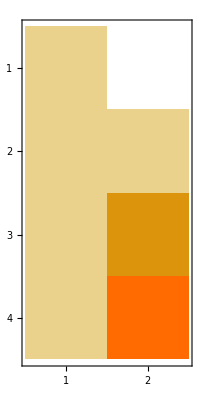

```mathematica
MatrixPlot[{{1,0},{1,1},{1,3},{1,5}}]
```

```mathematica
parabola=Fit[data,{1,x,x^2},x]
```

0.678392-0.266332 x+0.190955 x^2

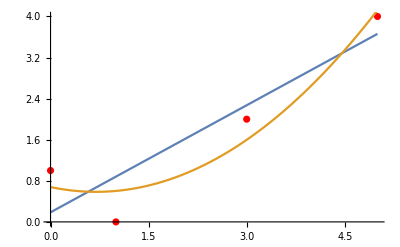

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,0,5}]]
```

```mathematica
m=N[HilbertMatrix[4]];
v=Range[4];
a=Fit[{m,v}]
```

{-64.,900.,-2520.,1820.}

```mathematica
HilbertMatrix[4]
```

{{1,1/2,1/3,1/4},{1/2,1/3,1/4,1/5},{1/3,1/4,1/5,1/6},{1/4,1/5,1/6,1/7}}

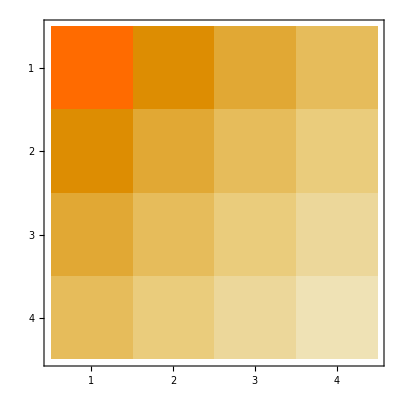

```mathematica
MatrixPlot[{{1,1/2,1/3,1/4},{1/2,1/3,1/4,1/5},{1/3,1/4,1/5,1/6},{1/4,1/5,1/6,1/7}}]
```

## 找到对给定数据集达到最佳拟合的公式

```mathematica
fp=Table[Prime[x],{x,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

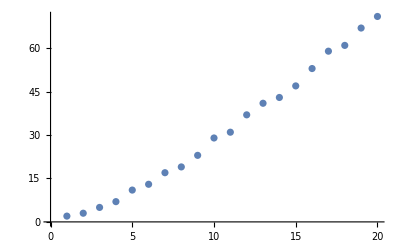

```mathematica
gp=ListPlot[fp]
```

```mathematica
Fit[fp,{1,x},x]
```

-7.67368+3.77368 x

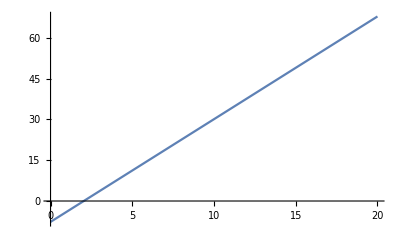

```mathematica
Plot[%,{x,0,20}]
```

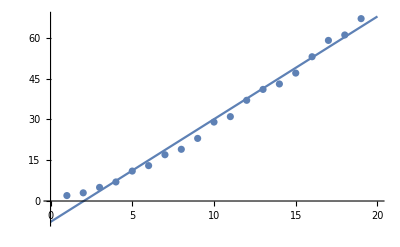

```mathematica
Show[%,gp]
```

```mathematica
Fit[fp,{1,x,x^2},x]
```

-1.92368+2.2055 x+0.0746753 x^2

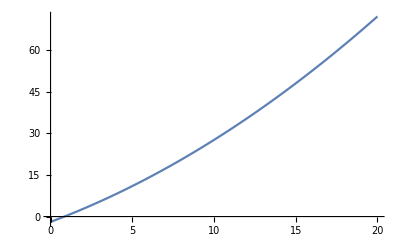

```mathematica
Plot[%,{x,0,20}]
.00
```

```mathematica
Show[%,gp]
```

Show::gcomb: Could not combine the graphics objects in Show[Null,].

Show[Null,-Graphics-]

```mathematica
Flatten[Table[{x,y,1+5 x-x y},{x,0,1,0.4},{y,0,1,0.4}],1]
```

{{0.,0.,1.},{0.,0.4,1.},{0.,0.8,1.},{0.4,0.,3.},{0.4,0.4,2.84},{0.4,0.8,2.68},{0.8,0.,5.},{0.8,0.4,4.68},{0.8,0.8,4.36}}

```mathematica
Fit[%,{1,x,y,x y},{x,y}]
```

1.+5. x+1.78489×10^-16 y-1. x y

```mathematica
FindFit[fp,a+b x+c Exp[x],{a,b,c},x]
```

FindFit::ivar: {-64.,900.,-2520.,1820.} is not a valid variable.

FindFit[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71},{-64.+c ⅇ^x+b x,900.+c ⅇ^x+b x,-2520.+c ⅇ^x+b x,1820.+c ⅇ^x+b x},{{-64.,900.,-2520.,1820.},b,c},x]

```mathematica
Fit[fp,{1,x,Exp[x]},x]
```

-6.78932+1.26883×10^-8 ⅇ^x+3.64309 x

```mathematica
FindFit[fp,a x Log[b+c x],{a,b,c},x]
```

FindFit::ivar: {-64.,900.,-2520.,1820.} is not a valid variable.

FindFit[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71},{-64. x Log[b+c x],900. x Log[b+c x],-2520. x Log[b+c x],1820. x Log[b+c x]},{{-64.,900.,-2520.,1820.},b,c},x]

```mathematica
FindFit[fp,{a x Log[b+c x],{0≤a≤1,0≤b≤1,c≥1}},{a,b,c},x]
```

FindFit::ivar: {-64.,900.,-2520.,1820.} is not a valid variable.

FindFit[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71},{{-64. x Log[b+c x],900. x Log[b+c x],-2520. x Log[b+c x],1820. x Log[b+c x]},{0≤{-64.,900.,-2520.,1820.}≤1,0≤b≤1,c≥1}},{{-64.,900.,-2520.,1820.},b,c},x]